```mathematica
data=Import["/Users/hkesari/Dropbox (Brown)/File Sep 11, 6 32 25 PM.txt","CSV"];
data=Table[ToExpression@StringSplit[data[[i,1]],";"],{i,2,Length@data}]
```

{{0,0.00103,-0.000963,-0.008225},{1,0.001649,0.001555,-0.009064},{2,-0.001236,-0.000607,-0.007385},{3,0.000826,-0.000744,-0.012909},{4,0.001368,-0.000407,-0.01007},{5,0.001452,0.00159,-0.006833},{6,0.000213,-0.000137,-0.009309},{7,-0.000845,-0.001371,-0.00955},{8,-0.000113,0.000363,-0.007356},{9,0.001483,0.000637,-0.009093},{10,-0.000396,-0.00015,-0.009},{11,0.001201,-0.00046,-0.007141},{12,-0.001046,0.000979,-0.011108},{13,-0.000709,0.001867,-0.011077},{14,0.000794,-0.000566,-0.008315},{15,-0.002136,-0.000114,-0.008576},{16,-0.000338,-0.001461,-0.008698},{17,-0.001748,0.000168,-0.00917},{18,-0.037496,0.037771,-0.011806},{19,-0.064778,0.002081,-0.015966},{20,-0.077255,0.141413,-0.004801},{21,-0.191669,0.129818,-0.008602},{22,-0.139627,0.10799,-0.010516},{23,-0.030382,0.067173,-0.008592},{24,0.008056,0.071167,-0.008516},{25,-0.005368,0.066245,-0.010234},{26,0.035788,0.084119,-0.006049},{27,-0.024886,0.174633,-0.010403},{28,0.081142,0.065645,-0.00702},{29,0.077207,0.0431,-0.006671},{30,0.09806,-0.00547,-0.007825},{31,0.272461,-0.199051,-0.006015},{32,0.279458,-0.209033,-0.004644},{33,0.413792,-0.452422,-0.012547},{34,0.288282,-0.112244,-0.011291},{35,0.365098,-0.354638,-0.007452},{36,0.302123,-0.249549,-0.009718},{37,0.262319,-0.159392,-0.009635},{38,0.275201,-0.06344,-0.012971},{39,0.202634,-0.156482,-0.011239},{40,0.037965,-0.07978,-0.006269},{41,0.093809,0.013777,-0.010621},{42,0.08146,0.117756,-0.010098},{43,0.026336,0.121336,-0.005283},{44,-0.188885,0.219635,-0.010382},{45,-0.382531,0.281489,-0.009579},{46,-0.45545,0.417806,-0.006651},{47,-0.193964,0.206594,-0.018725},{48,-0.285745,0.263326,-0.014741},{49,-0.211967,0.274533,-0.008734},{50,-0.25,0.235369,-0.01325},{51,-0.119674,0.176167,-0.007797},{52,-0.006963,0.086027,-0.01145},{53,0.01185,0.11379,-0.003535},{54,0.04828,0.119174,-0.008697},{55,0.081211,0.005078,-0.007781},{56,0.011012,0.025936,-0.006043},{57,-0.00318,0.033113,-0.010109},{58,0.173902,-0.096819,-0.010277},{59,0.202635,-0.08627,-0.007526},{60,0.428965,-0.22994,-0.006446},{61,0.427404,-0.230696,-0.006462},{62,0.659062,-0.473914,-0.006675},{63,0.495446,-0.149108,-0.003417},{64,0.470767,-0.488372,-0.011216},{65,0.490935,-0.365477,-0.011223},{66,0.454883,-0.187196,-0.007819},{67,0.259282,-0.120548,-0.000246},{68,0.170111,-0.106933,-0.009724},{69,0.093312,0.083872,-0.005259},{70,0.164411,0.07346,-0.014451},{71,-0.000542,0.164783,-0.008524},{72,0.037781,0.275012,-0.008783},{73,-0.230834,0.334915,-0.0059},{74,-0.484155,0.454552,-0.007114},{75,-0.529048,0.503913,-0.002876},{76,-0.489818,0.464442,-0.005104},{77,-0.416967,0.401115,-0.018058},{78,-0.320713,0.393176,-0.005329},{79,-0.297748,0.416912,-0.012162},{80,-0.33869,0.389493,-0.010919},{81,-0.153934,0.267564,-0.004765},{82,-0.123651,0.279334,-0.010272},{83,-0.024423,0.252783,-0.01978},{84,0.306858,0.0075,-0.014485},{85,0.467807,-0.098997,-0.005476},{86,0.705698,-0.301139,-0.00684},{87,0.591065,-0.33924,-0.012547},{88,0.509551,-0.424958,-0.012029},{89,0.573924,-0.383999,-0.012574},{90,0.698657,-0.456883,-0.011891},{91,0.488862,-0.416043,-0.009565},{92,0.384318,-0.193006,-0.008193},{93,0.452679,-0.16899,-0.005839},{94,0.208464,-0.010287,-0.010389},{95,0.116173,-0.078343,-0.00784},{96,0.047992,0.038991,-0.010701},{97,-0.028685,0.118223,-0.008852},{98,-0.095861,0.276851,-0.007091},{99,-0.291756,0.481902,-0.007356},{100,-0.425587,0.425962,-0.006896},{101,-0.362223,0.251241,-0.00698},{102,-0.120381,0.196627,-0.004695},{103,0.00663,-0.027923,-0.009822},{104,0.01876,-0.048722,-0.015296},{105,0.004425,-0.024897,-0.013226},{106,-0.014799,0.019473,-0.007998},{107,0.007137,-0.024742,-0.007892},{108,0.007476,-0.025195,-0.009326},{109,0.005963,-0.028339,-0.005313},{110,0.004591,-0.026383,-0.010481},{111,0.004653,-0.02101,-0.008647},{112,0.005939,-0.021336,-0.008301},{113,0.004363,-0.021639,-0.008687},{114,0.004544,-0.019537,-0.007634},{115,0.005922,-0.020064,-0.010373},{116,0.028978,-0.009224,0.034386},{117,0.00496,-0.020109,-0.017816}}

```mathematica
data[[;;,2]]
```

{0.00103,0.001649,-0.001236,0.000826,0.001368,0.001452,0.000213,-0.000845,-0.000113,0.001483,-0.000396,0.001201,-0.001046,-0.000709,0.000794,-0.002136,-0.000338,-0.001748,-0.037496,-0.064778,-0.077255,-0.191669,-0.139627,-0.030382,0.008056,-0.005368,0.035788,-0.024886,0.081142,0.077207,0.09806,0.272461,0.279458,0.413792,0.288282,0.365098,0.302123,0.262319,0.275201,0.202634,0.037965,0.093809,0.08146,0.026336,-0.188885,-0.382531,-0.45545,-0.193964,-0.285745,-0.211967,-0.25,-0.119674,-0.006963,0.01185,0.04828,0.081211,0.011012,-0.00318,0.173902,0.202635,0.428965,0.427404,0.659062,0.495446,0.470767,0.490935,0.454883,0.259282,0.170111,0.093312,0.164411,-0.000542,0.037781,-0.230834,-0.484155,-0.529048,-0.489818,-0.416967,-0.320713,-0.297748,-0.33869,-0.153934,-0.123651,-0.024423,0.306858,0.467807,0.705698,0.591065,0.509551,0.573924,0.698657,0.488862,0.384318,0.452679,0.208464,0.116173,0.047992,-0.028685,-0.095861,-0.291756,-0.425587,-0.362223,-0.120381,0.00663,0.01876,0.004425,-0.014799,0.007137,0.007476,0.005963,0.004591,0.004653,0.005939,0.004363,0.004544,0.005922,0.028978,0.00496}

```mathematica
data[[2;;]][[2]][[1]]
```

2

```mathematica
Import["/Users/hkesari/Dropbox (Brown)/File Sep 11, 6 10 39 PM.xml","Elements"]
```

{CDATA,Comments,EmbeddedDTD,Plaintext,Tags,XMLElement,XMLObject}

{{index,x,y,z},{0,-0.001214,0.007307,-0.015184},{1,0.007071,0.005230,0.016026},{2,0.004593,-0.005560,0.000446},{3,0.000220,0.004933,-0.002313},{4,0.008948,-0.009127,-0.011172},{5,0.004508,0.009189,0.008258},{6,-0.004770,-0.005533,0.002486},2224,{2231,-0.047913,0.039413,-0.024310},{2232,0.005848,0.007676,0.005681},{2233,-0.024577,0.005658,0.002599},{2234,-0.032618,-0.002186,0.004101},{2235,0.013084,-0.004996,0.050065},{2236,-0.054269,0.054920,-0.051079},{2237,-0.014340,0.026894,-0.040823}}
 |  |  |  |

StringTake[string,n] gives a string containing the first n characters in "string". 
StringTake[string,-n] gives the last n characters in "string". 
StringTake[string,{n}] gives the n^th character in "string". 
StringTake[string,{m,n}] gives characters m through n in "string". 
StringTake[string,{spec_1,spec_2,…}] gives a list of the substrings specified by the spec_i.
StringTake[{s_1,s_2,…},spec] gives the list of results for each of the s_i.

```mathematica
ListLinePlot[{data[[;;,{1,2}]],data[[;;,{1,3}]],data[[;;,{1,4}]]},PlotRange->Full]
```

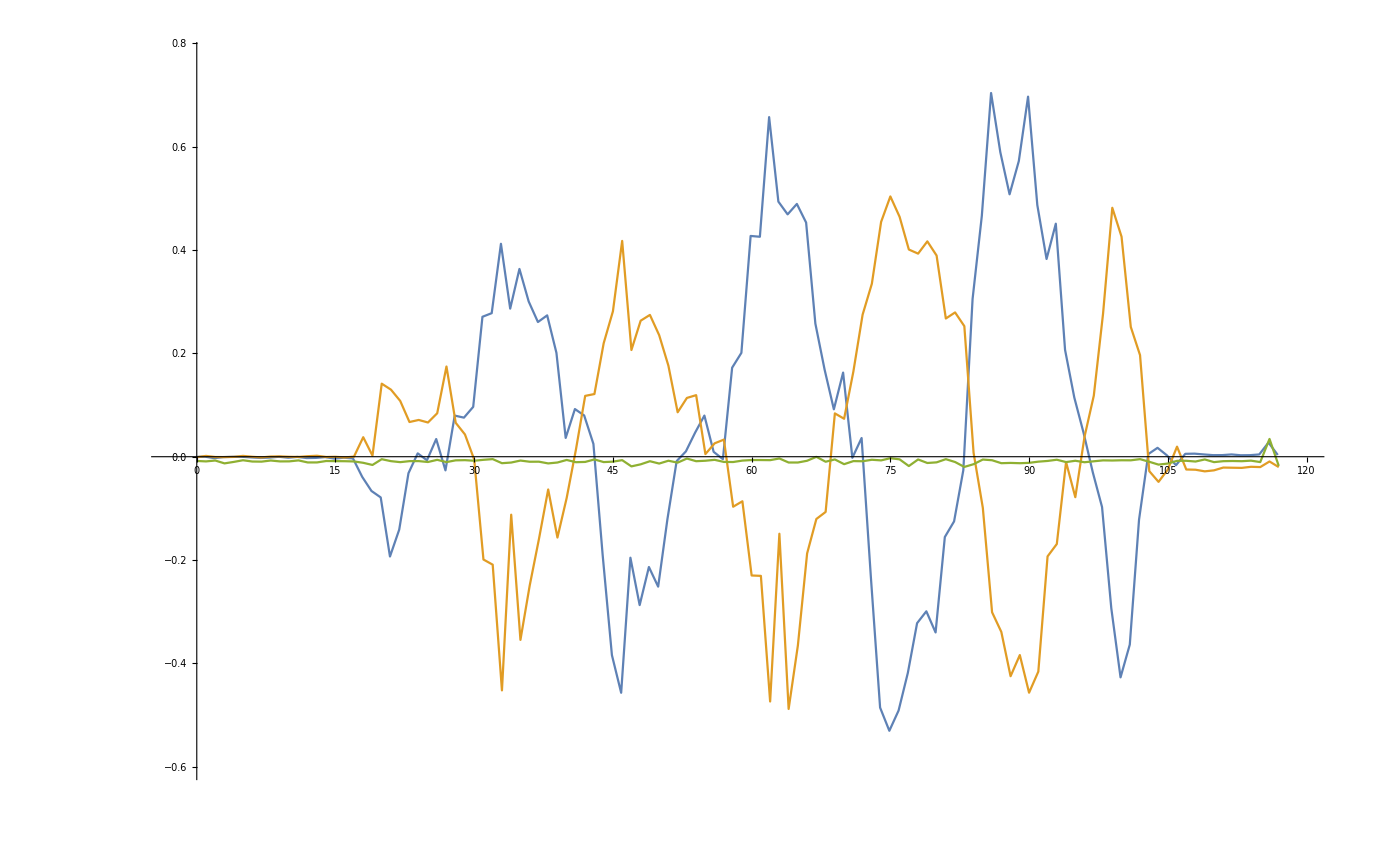

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points {1,y_1},{2,y_2},…. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{data_1,data_2,…}] plots data from all the data_i.
ListPlot[{…,w[data_i,…],…}] plots data_i with features defined by the symbolic wrapper w.

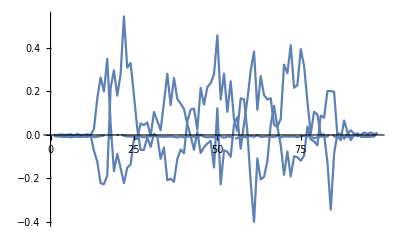

```mathematica
Show[data[[;;,2]]//ListLinePlot,
data[[;;,3]]//ListLinePlot,
data[[;;,4]]//ListLinePlot]
```